```mathematica
[-Graphics-](https://mipt.ru/education/chair/theoretical_mechanics/courses/haos-i-kotiki.php)[-Graphics-](https://t.me/miptdesign)-Graphics-mailto: efimov.ss@phystech.eduNonemailto: efimov.ss@phystech.eduHyperlinkHyperlinkActive
```

```mathematica
"TeX"paclet:tutorial/GeneratingAndImportingTeX
```

TeXForm[HoldForm[]]
MaTeX[]
ToExpression[,TeXForm]

## WM → TEX

```mathematica
TeXForm[(x 4^(1/3)√(1+x^5))/5]
```

\frac{1}{5} 2^{2/3} x \sqrt{x^5+1}

Можно также использовать функцию Copy As для непосредственного перенесения формул в TeX

## TEX → WM

```mathematica
ToExpression["\\sqrt{1+x^2}",TeXForm]
```

√(1+x^2)

## MaTeX (TEX in WM)

```mathematica
["Установка MaTeX"](https://github.com/szhorvat/MaTeX)
```

запустить скрипт и следовать дальнейшим инструкциям для связи с pdflaTeX и GhostScript:

```mathematica
Needs["PacletManager`"];
pacletfile=URLDownload["https://github.com/szhorvat/MaTeX/releases/download/v1.7.8/MaTeX-1.7.8.paclet"]⟦1⟧;
PacletInstall[pacletfile];
DeleteFile[pacletfile];
Needs["MaTeX`"];
```

pdfLaTeX is not found at

Please configure pdfLaTeX using ConfigureMaTeX["pdfLaTeX" -> "path to pdflatex executable…"]

Ghostscript is not found at

Please configure Ghostscript using ConfigureMaTeX["Ghostscript" -> "path to gs executable…"]

Click here for documentation on configuring MaTeX.

#### Использование

```mathematica
Needs["MaTeX`"];
TeX1=MaTeX[TeXForm[HoldForm[(x 4^(1/3)√(1+x^5))/5]]]
```

-Graphics-

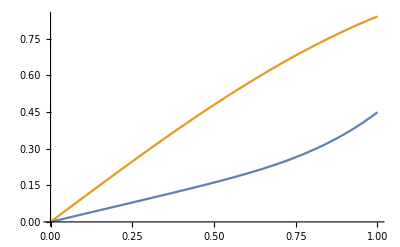

```mathematica
Plot[{(x 4^(1/3)√(1+x^5))/5,Sin[x]},{x,0,1},PlotLegends->Placed[{TeX1,MaTeX@TeXForm@HoldForm[Sin[x]]},Above]]
```